```mathematica
Needs["Screening`",NotebookDirectory[]<>"../packages/Screening.wl"]
Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
```

```mathematica
GetProbeFunctions[]/.{Private`u->z,Private`z->z}
```

<|cap→(ⅇ^(-(4 Private`mi βi Max[(Private`mj z z)/(Private`mi),zesci^2])/(Private`mj βj))-ⅇ^(-(4 Private`mi βi Min[1/4 (z+(Private`mj z)/(Private`mi))^2,(Private`mj z z)/(Private`mi)+zesci^2])/(Private`mj βj))) ni √(2/π) √(Private`mi βi) HeavisideTheta[-zesci^2+1/4 ((Private`mj z)/(Private`mi)+Abs[z])^2],evap→(ⅇ^(-(4 Private`mi βi Max[0,zesci^2-(Private`mj z Abs[z])/(Private`mi)])/(Private`mj βj))-ⅇ^(-(4 Private`mi βi Min[zesci^2,1/4 ((Private`mj z)/(Private`mi)-Abs[z])^2])/(Private`mj βj))) ni √(2/π) √(Private`mi βi) HeavisideTheta[-zesci^2+1/4 ((Private`mj z)/(Private`mi)+Abs[z])^2]|>

```mathematica
FeNucCoeffs
```

<|name→Fe,a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26,nI→1.402×10^29,β→1.32379×10^19|>

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.174811}. NIntegrate obtained 5.6426×10^24 and 8.46106×10^20 for the integral and error estimates.

5.6426×10^24

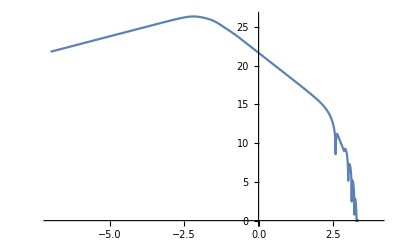

```mathematica
Association@Table[{#[[i]]["name"]->GetNuclearEarthTargetResponses[#[[i]]]},{i,Length[#]}]&@{FeNucCoeffs,SiNucCoeffs};
NIntegrate[%["Fe"]/.Private`z->z,{z,0,100}]
Plot[Log10@%%["Fe"]/.Private`z->10^logz,{logz,-7,4}]
```

#### Earth parameters

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

```mathematica
FeNucCoeffs
SiNucCoeffs
MgNucCoeffs
ONucCoeffs
```

<|a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26,nI→1.402×10^29,β→1.32379×10^19|>

<|a→{6.2915,3.0353,1.9891,1.541},b→{2.4386,32.3337,0.6785,81.6937},c→1.1407,Z→13.9976,A→28,rn→3.46171×10^-15,mN→4.648×10^-26,nI→4.995×10^28,β→2.76063×10^19|>

<|a→{5.4204,2.1735,1.2269,2.3073},b→{2.8275,79.2611,0.38,7.1937},c→0.8584,Z→11.9865,A→24,rn→3.28833×10^-15,mN→3.984×10^-26,nI→4.362×10^28,β→2.76063×10^19|>

<|a→{3.0485,2.2868,1.5463,0.867},b→{13.2771,5.7011,0.3239,32.9089},c→0.2508,Z→7.9994,A→16,rn→2.87262×10^-15,mN→2.656×10^-26,nI→1.435×10^29,β→2.76063×10^19|>

### Scrap

#### Electronic structure functions

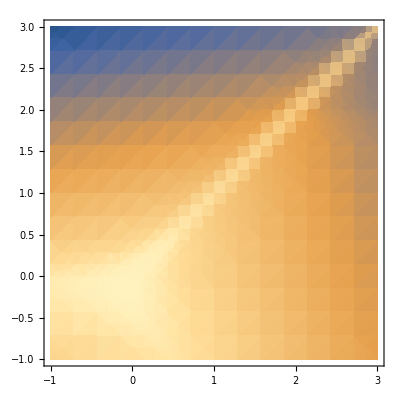

```mathematica
DensityPlot[Log10@StructureFunctionuz1osc[10^u,10^z,FeTotalparams[[1]]],{u,-1,3},{z,-1,3}]
```

```mathematica
Log10@StructureFunctionuz1osc[10^u,10^z,FeTotalparams[[1]]]
```

#### Compare static nuclear and finite temperature plasma approx for nuclear

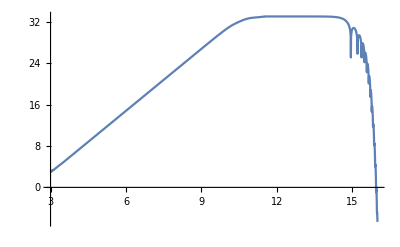

```mathematica
Plot[Log10[2 π  #["nI"]FormFactors`Zeff[10^q,#]^2 &@FeNucCoeffs],{q,3,16},PlotLabel->"S_nuc(ω,q)"]
```

```mathematica
VCoul[q_]:= ((("e")^2)/(q^2 "ϵ0"))(*no kappa included here*)
```

Nuclear in ω z variables

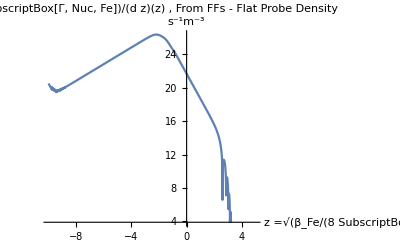

```mathematica
"Nuclear in ω z variables"
(*(√((8 #["mN"])/(#["β"]("ℏ")^2))) (*from q->z jac*)q/("ℏ"(2π)^2) VCoul[q]^2 2 π  #["nI"]FormFactors`Zeff[q,#]^2 /.{ω->("ℏ"q^2)/(2 #["mN"])}/.{q->z √((8 #["mN"])/(#["β"]("ℏ")^2))}&@FeNucCoeffs/.SIConstRepl*)
(√((8 #["mN"])/(#["β"]("ℏ")^2))) (*from q->z jac*)q/("ℏ"(2π)^2) (1/("ℏ") (*from E->ω in δ fn*))VCoul[q]^2 2 π  #["nI"]FormFactors`Zeff[q,#]^2 /.{ω->("ℏ"q^2)/(2 #["mN"])}/.{q->z √((8 #["mN"])/(#["β"]("ℏ")^2))}&@FeNucCoeffs/.SIConstRepl;
Plot[Log10[%/.z->10^logz],{logz,-10,5},PlotLabel->"(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From FFs - Flat Probe Density",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [ ]","s^-1m^-3"}]
```

Nuclear w naive nuclear screening (no electrons) in u z variables on the static line

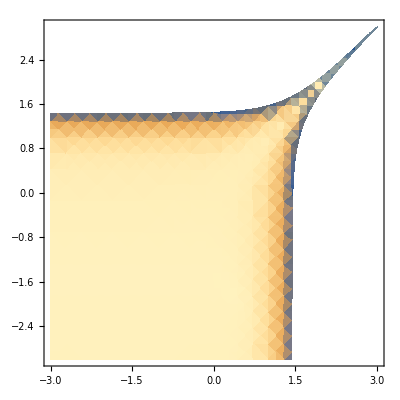

```mathematica
"Nuclear w naive nuclear screening (no electrons) in u z variables on the static line"
(1/((2 π)^2"ℏ")4/("ℏ"#["β"])(*from jac*))(*((#["β"]"ℏ")/4 (*from jac*))*)GetTargetResponses[]["therm"]/.{Private`z->z,Private`u->u}(*/.{(*z->(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1 q,*)u->ω/q √((#["mN"] #["β"])/2)}*)(*/.{ω->("ℏ"q^2)/(2 #["mN"])}*)(*/.{q->z √((8 #["mN"])/(#["β"]("ℏ")^2))}*)/.{"zD"->√(2 #["nI"]#["β"] ("e")^2/("ϵ0"))(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1}&@FeNucCoeffs/.SIConstRepl;
Quiet@DensityPlot[Log10[%/.{z->10^logz,u->10^logu}],{logu,-3,5},{logz,-3,5},PlotRange->All]
```

Nuclear w naive nuclear screening (no electrons) in ω z variables on the static line

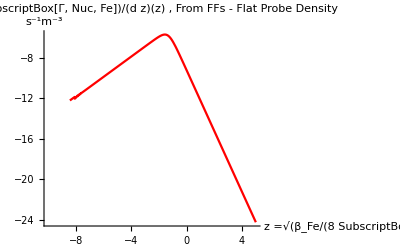

```mathematica
"Nuclear w naive nuclear screening (no electrons) in ω z variables on the static line"
(1/((2 π)^2"ℏ") (√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1(*from jac*))(*((#["β"]"ℏ")/4 (*from jac*))*)GetTargetResponses[]["therm"]/.{Private`z->z,Private`u->u}/.{(*z->(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1 q,*)u->ω/q √((#["mN"] #["β"])/2)}/.{ω->("ℏ"q^2)/(2 #["mN"])}/.{q->z √((8 #["mN"])/(#["β"]("ℏ")^2))}/.{"zD"->√(2 #["nI"]#["β"] ("e")^2/("ϵ0"))(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1}&@FeNucCoeffs/.SIConstRepl;
Quiet@Plot[Log10[%/.z->10^logz],{logz,-10,5},PlotStyle->Red,PlotLabel->"(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From FFs - Flat Probe Density",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [ ]","s^-1m^-3"}]
```

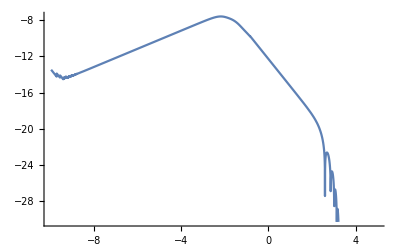
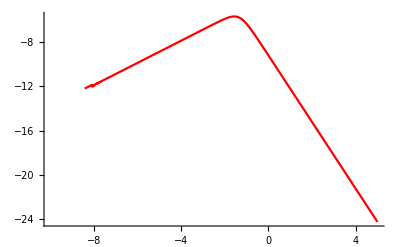
```mathematica
Show[{-Graphics-,-Graphics-},PlotRange->{-25,0}]
```

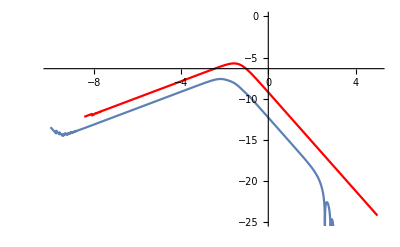

```mathematica
"mN"/.FeNucCoeffs
% ("c")^2/("JpereV")/.SIConstRepl
```

9.296×10^-26

5.22247×10^10

#### Scrap - Integrate the plasma response for the non-degenerate nuclear model

```mathematica
nucresponseRPAofzandu = 1/(π^2("ℏ")^2#["β"])(*(1/((2 π)^2"ℏ") (√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1(*from jac*))*)(*(√((#["β"]("ℏ")^2)/(8 #["mN"]))(*from z -> q jac*))*)(*((#["β"]"ℏ")/4 (*from(u,z)->(ω,q) jac*))*)GetTargetResponses[]["therm"]/.{Private`z->z,Private`u->u}(*/.{(*z->(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1 q,*)u->ω/q √((#["mN"] #["β"])/2)}/.{ω->("ℏ"q^2)/(2 #["mN"])}*)/.{q->z √((8 #["mN"])/(#["β"]("ℏ")^2))}/.{"zD"->√(2 #["nI"]#["β"] ("e")^2/("ϵ0"))(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1}&@FeNucCoeffs/.SIConstRepl
(*Plot[Log10[%/.z->10^logz],{logz,-10,5}]*)
```

(1.20235×10^18 (ⅇ^(-(u-z)^2) π-ⅇ^(-(u+z)^2) π))/((1-ⅇ^(-4 u z)) z^3 ((9.0683×10^-8 (ⅇ^(-(u-z)^2) π-ⅇ^(-(u+z)^2) π)^2)/z^6+(1+(0.000301136 (-2 √π DawsonF[u-z]+2 √π DawsonF[u+z]))/z^3)^2))

(1.86858×10^-10 (ⅇ^(-(u-z)^2) π-ⅇ^(-(u+z)^2) π))/((1-ⅇ^(-4 u z)) z^3 ((9.0683×10^-8 (ⅇ^(-(u-z)^2) π-ⅇ^(-(u+z)^2) π)^2)/z^6+(1+(0.000301136 (-2 √π DawsonF[u-z]+2 √π DawsonF[u+z]))/z^3)^2))

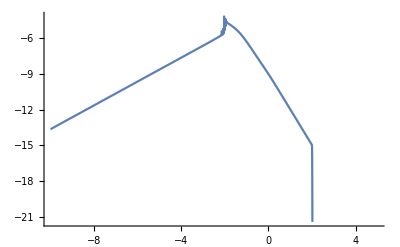

```mathematica
Plot[Log10[NIntegrate[%/.z->#,{u,0,100}]&[10^logz]],{logz,-10,5}]
```

```mathematica
(*Plot[Log10[%/.z->10^logz],{logz,-10,5}]*)

Plot[Log10[NIntegrate[%/.z->#,{u,0,100}]&[10^logz]],{logz,-10,5}]
```

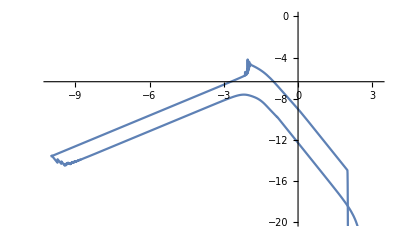

```mathematica
Show[{-Graphics-,-Graphics-},PlotRange->{-20,0}]
```

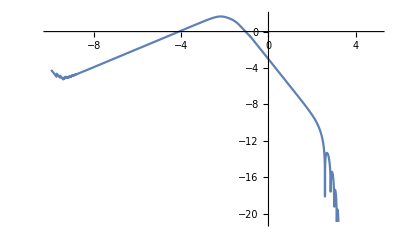
```mathematica
Show[{-Graphics-,-Graphics-},PlotRange->{-20,0}]
```

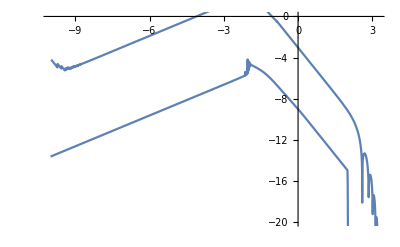

#### corrections

Nuclear w naive nuclear screening (no electrons) in u z variables on the static line

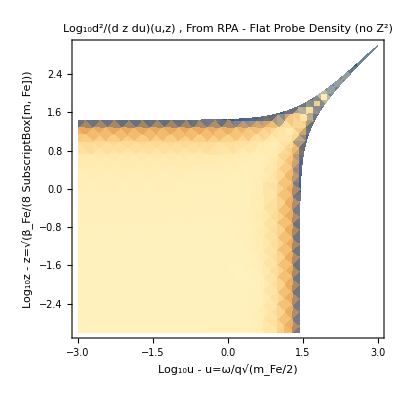

```mathematica
"Nuclear w naive nuclear screening (no electrons) in u z variables on the static line"
(1/((2 π)^2"ℏ")4/("ℏ"#["β"])(*from jac*))(*((#["β"]"ℏ")/4 (*from jac*))*)GetTargetResponses[]["therm"]/.{Private`z->z,Private`u->u}(*/.{(*z->(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1 q,*)u->ω/q √((#["mN"] #["β"])/2)}*)(*/.{ω->("ℏ"q^2)/(2 #["mN"])}*)(*/.{q->z √((8 #["mN"])/(#["β"]("ℏ")^2))}*)/.{"zD"->√(2 #["nI"]#["β"] ("e")^2/("ϵ0"))(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1}&@FeNucCoeffs/.SIConstRepl;
Quiet@DensityPlot[Log10[%/.{z->10^logz,u->10^logu}],{logu,-3,5},{logz,-3,5},PlotRange->All,PlotLabel->"Log_10d^2/(d z du)(u,z) , From RPA - Flat Probe Density (no Z^2)",FrameLabel->{"Log_10u - u=ω/q√(m_Fe/2)","Log_10z - z=√(β_Fe/(8 SubscriptBox[m, Fe]))"}]
```

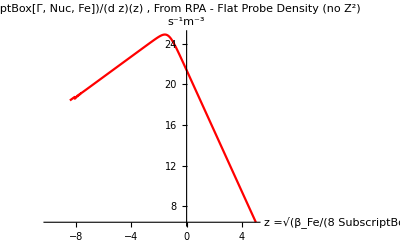

```mathematica
(*Note that this is assuming that the electrons are doing the screening so there's no Z enhancement int he debye momentum*)
βresc = 1;
(#["Z"])^2(1/(( π)^2("ℏ")^2 βresc#["β"]) (*from jac*))(*((#["β"]"ℏ")/4 (*from jac*))*)GetTargetResponses[]["therm"]/.{Private`z->z,Private`u->u}/.{(*z->(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1 q,*)u->ω/q √((#["mN"]βresc #["β"])/2)}/.{ω->("ℏ"q^2)/(2 #["mN"])}/.{q->z √((8 #["mN"])/(βresc#["β"]("ℏ")^2))}/.{"zD"->√(2 #["nI"]βresc#["β"] ("e")^2/("ϵ0"))(√((8 #["mN"])/(βresc#["β"]("ℏ")^2)))^-1}&@FeNucCoeffs/.SIConstRepl;
Quiet@Plot[Log10[%/.z->10^logz],{logz,-10,5},PlotStyle->Red,PlotLabel->"(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From RPA - Flat Probe Density (no Z^2)",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [Log_10]","s^-1m^-3"}]
```

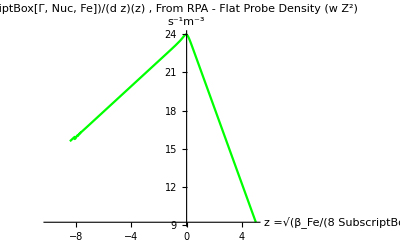

```mathematica
(*Note that this is assuming that the electrons are doing the screening so there's no Z enhancement int he debye momentum*)
βresc = 1;
(#["Z"])^2(1/(( π)^2("ℏ")^2 βresc#["β"]) (*from jac*))(*((#["β"]"ℏ")/4 (*from jac*))*)GetTargetResponses[]["therm"]/.{Private`z->z,Private`u->u}/.{(*z->(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1 q,*)u->ω/q √((#["mN"]βresc #["β"])/2)}/.{ω->("ℏ"q^2)/(2 #["mN"])}/.{q->z √((8 #["mN"])/(βresc#["β"]("ℏ")^2))}/.{"zD"->√(2 #["nI"](#["Z"])^2 βresc#["β"] ("e")^2/("ϵ0"))(√((8 #["mN"])/(βresc#["β"]("ℏ")^2)))^-1}&@FeNucCoeffs/.SIConstRepl;
Quiet@Plot[Log10[%/.z->10^logz],{logz,-10,5},PlotStyle->Green,PlotLabel->"(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From RPA - Flat Probe Density (w Z^2)",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [Log_10]","s^-1m^-3"}]
```

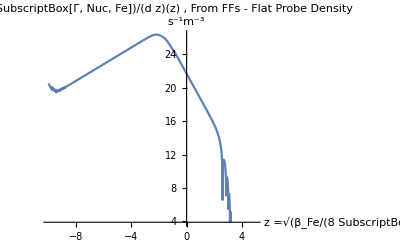

```mathematica
(√((8 #["mN"])/(#["β"]("ℏ")^2))) (*from q->z jac - no ω->u jac because of the δ fn in ω*)q/("ℏ"(2π)^2) (1/("ℏ") (*from E->ω in δ fn*))VCoul[q]^2 2 π  #["nI"]FormFactors`Zeff[q,#]^2 /.{ω->("ℏ"q^2)/(2 #["mN"])}/.{q->z √((8 #["mN"])/(#["β"]("ℏ")^2))}&@FeNucCoeffs/.SIConstRepl;
Plot[Log10[%/.z->10^logz],{logz,-10,5},PlotLabel->"Log_10(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From FFs - Flat Probe Density",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [Log_10]","s^-1m^-3"}]
```

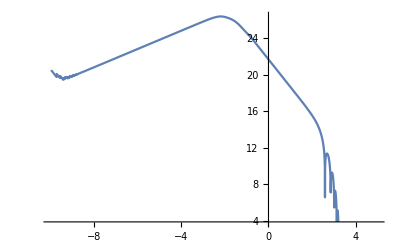
```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-},PlotRange->{15,30},PlotLabel->"Log_10(d SubscriptBox[Γ, Nuc, Fe])/(d z) - comparisons"]
```

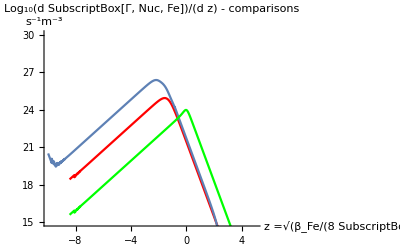

the u<<1 limit needs to be done with the electron v_F speeds since they are what are doing the screening in the nucleus.

#### Electronic screening with nuclear scattering

```mathematica
("ωedgei")/z √((#["mN"]βresc #["β"])/2)(√((8 #["mN"])/(βresc#["β"]("ℏ")^2)))^-1&@FeNucCoeffs/.SIConstRepl/.FeTotalparams
```

{0.211068/z,0.00230044/z,0.105784/z,0.0530178/z,380.721/z,3836.9/z}

no inner shells

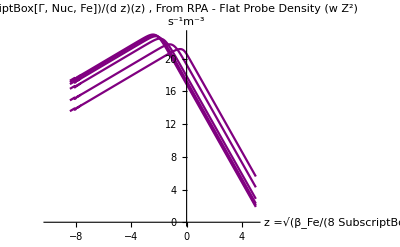

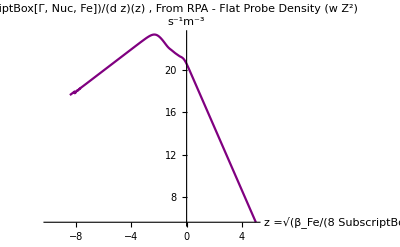

```mathematica
"no inner shells"
βresc = 1;
((*HeavisideTheta[1-("ωedgei")/z √((#["mN"]βresc #["β"])/2)(√((8 #["mN"])/(βresc#["β"]("ℏ")^2)))^-1]*)(*If[Evaluate["ωedgei"√((#["mN"]βresc #["β"])/2)(√((8 #["mN"])/(βresc#["β"]("ℏ")^2)))^-1]>0.003,HeavisideTheta[1-("ωedgei")/z √((#["mN"]βresc #["β"])/2)(√((8 #["mN"])/(βresc#["β"]("ℏ")^2)))^-1],1](#["Z"])^2*)(1/(( π)^2("ℏ")^2 βresc#["β"]) (*from jac*))(*((#["β"]"ℏ")/4 (*from jac*))*)GetTargetResponses[]["therm"]/.{Private`z->z,Private`u->u}/.{(*z->(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1 q,*)u->ω/q √((#["mN"]βresc #["β"])/2)}/.{ω->("ℏ"q^2)/(2 #["mN"])}/.{q->z √((8 #["mN"])/(βresc#["β"]("ℏ")^2))}/.{"zD"->"qF"(√((8 #["mN"])/(βresc#["β"]("ℏ")^2)))^-1}&@FeNucCoeffs/.SIConstRepl)/.FeTotalparams;
(*%/.FeTotalparams[[;;-3]]*)
Quiet@Plot[Log10[%/.z->10^logz],{logz,-10,5},PlotStyle->Purple,PlotLabel->"(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From RPA - Flat Probe Density (w Z^2)",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [Log_10]","s^-1m^-3"}]
Quiet@Plot[Log10[Total@%%/.z->10^logz],{logz,-10,5},PlotStyle->Purple,PlotLabel->"(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From RPA - Flat Probe Density (w Z^2)",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [Log_10]","s^-1m^-3"}]
```

w inner shells

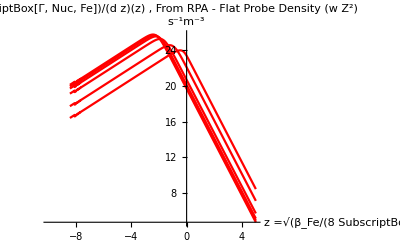

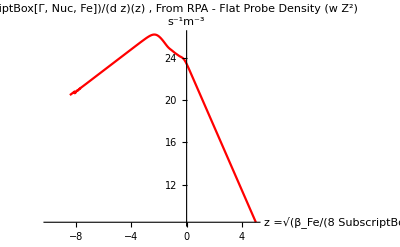

```mathematica
"w inner shells"
βresc = 1;
(#["Z"])^2(1/(( π)^2("ℏ")^2 βresc#["β"]) (*from jac*))(*((#["β"]"ℏ")/4 (*from jac*))*)GetTargetResponses[]["therm"]/.{Private`z->z,Private`u->u}/.{(*z->(√((8 #["mN"])/(#["β"]("ℏ")^2)))^-1 q,*)u->ω/q √((#["mN"]βresc #["β"])/2)}/.{ω->("ℏ"q^2)/(2 #["mN"])}/.{q->z √((8 #["mN"])/(βresc#["β"]("ℏ")^2))}/.{"zD"->"qF"(√((8 #["mN"])/(βresc#["β"]("ℏ")^2)))^-1}&@FeNucCoeffs/.SIConstRepl/.FeTotalparams;
Quiet@Plot[Log10[%/.z->10^logz],{logz,-10,5},PlotStyle->Red,PlotLabel->"(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From RPA - Flat Probe Density (w Z^2)",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [Log_10]","s^-1m^-3"}]
Quiet@Plot[Log10[Total@%%/.z->10^logz],{logz,-10,5},PlotStyle->Red,PlotLabel->"(d SubscriptBox[Γ, Nuc, Fe])/(d z)(z) , From RPA - Flat Probe Density (w Z^2)",AxesLabel->{"z =√(β_Fe/(8 SubscriptBox[m, Fe])) [Log_10]","s^-1m^-3"}]
```

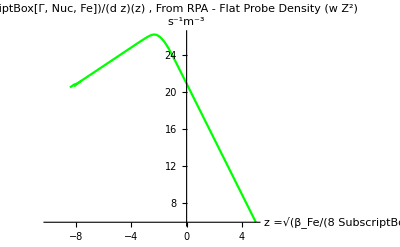
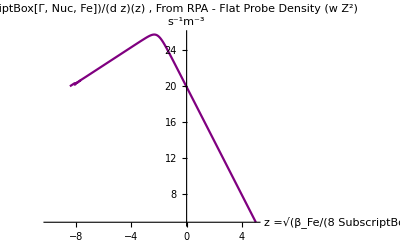
```mathematica
"This drops the inner shells, and shows that the low energy tail and peak predicted by the form factor are captured by the outer electron shells in the limit u->0. If the momentum range used to construct the form factor falls below the peak, this also tells us that the inner shells are not being probed by the form factor data, and our results should be trusted more."
"This also shows us why the electrons didn't contribute. The integral is dominated by u, z <<1. So we often fall below the cutoff of the inner electron shells for the silicates."
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

This drops the inner shells, and shows that the low energy tail and peak predicted by the form factor are captured by the outer electron shells in the limit u->0. If the momentum range used to construct the form factor falls below the peak, this also tells us that the inner shells are not being probed by the form factor data, and our results should be trusted more.

This also shows us why the electrons didn't contribute. The integral is dominated by u, z <<1. So we often fall below the cutoff of the inner electron shells for the silicates.

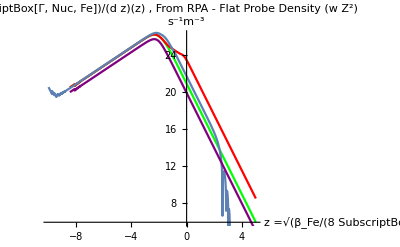

#### Run Pipeline

```mathematica
Clear[δScanList]
δScanList = {<|"δ"-> 10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"-> 1.5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"-> 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>,
<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,
<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>};
```

```mathematica
(*
Add in:

<|"δ"-> 10^-3,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_07_2025_0p999\\PDictList\\PDictList_ϕE_99p9_pcnt_0"|>
*)
```

Todo: 

correct conversion between ϕfrac and δ (done)
restrict δ to less than 0.75 everywhere (done)
set rmax to 0 below the minimum δ value (no need to do this.)
unit test the root finding (done)
rerun (done)

```mathematica
(1-ϕfrac)vescE^2/2 == vesc^2/2 (*for ϕfrac != 0*)
δ vescE^2/2== vesc^2/2
```

We have written the potential in the capture code so that it is flat for ϕfrac != 0 but is just grav otherwise. So for ϕfrac = 0 δ=1.5, otherwise δ=1-ϕfrac

```mathematica
ScanOverUnfixedParameters[δScanList,{1},{0.01}]
```

Running: {1,1,0.01}

```mathematica
(*files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\18_07_2025\\δDicts"];(*without plasma rates*)*)
files =FileNames["*.dat","C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\08_01_2026\\δDicts"]; (*with plasma rates*)
truthtabletest=Monitor[Quiet@Table[file=ReadIt[files[[f]]];GetδDictTruth[file],{f,1(*Length@files*)}],f];
```

```mathematica
{"κ","v0","mpD","meD","βD","δ"}/.truthtabletest
```

{{{{1/100000000000000,20000,1.78×10^-30,1.78×10^-34,0.00997899},{1/100000000000000,20000,1.78×10^-29,1.78×10^-33,0.749392},{1/100000000000000,20000,1.78×10^-28,1.78×10^-32,0.0000100001},{1/100000000000000,20000,1.78×10^-27,1.78×10^-31,0.749392},{1/100000000000000,20000,1.78×10^-26,1.78×10^-30,0.749392},{1/100000000000000,20000,1.78×10^-25,1.78×10^-29,0.492976},{1/100000000000000,20000,1.78×10^-24,1.78×10^-28,0.0619045},{1/100000000000000,20000,1.78×10^-23,1.78×10^-27,0.057922},{1/100000000000000,20000,1.78×10^-22,1.78×10^-26,0.38483},{1/100000000000000,20000,1.78×10^-21,1.78×10^-25,0.749392}},{{1/10000000000000,20000,1.78×10^-30,1.78×10^-34,0.00997899},{1/10000000000000,20000,1.78×10^-29,1.78×10^-33,0.749392},{1/10000000000000,20000,1.78×10^-28,1.78×10^-32,0.0000100001},{1/10000000000000,20000,1.78×10^-27,1.78×10^-31,0.749392},{1/10000000000000,20000,1.78×10^-26,1.78×10^-30,0.749392},{1/10000000000000,20000,1.78×10^-25,1.78×10^-29,0.41309},{1/10000000000000,20000,1.78×10^-24,1.78×10^-28,0.0494293},{1/10000000000000,20000,1.78×10^-23,1.78×10^-27,0.0384168},{1/10000000000000,20000,1.78×10^-22,1.78×10^-26,0.0417863},{1/10000000000000,20000,1.78×10^-21,1.78×10^-25,0.749392}},{{1/1000000000000,20000,1.78×10^-30,1.78×10^-34,0.00997899},{1/1000000000000,20000,1.78×10^-29,1.78×10^-33,0.749392},{1/1000000000000,20000,1.78×10^-28,1.78×10^-32,0.0000100001},{1/1000000000000,20000,1.78×10^-27,1.78×10^-31,0.749392},{1/1000000000000,20000,1.78×10^-26,1.78×10^-30,0.749392},{1/1000000000000,20000,1.78×10^-25,1.78×10^-29,0.381737},{1/1000000000000,20000,1.78×10^-24,1.78×10^-28,0.0323587},{1/1000000000000,20000,1.78×10^-23,1.78×10^-27,0.00345514},{1/1000000000000,20000,1.78×10^-22,1.78×10^-26,0.0230123},{1/1000000000000,20000,1.78×10^-21,1.78×10^-25,0.0394799}},{{1/100000000000,20000,1.78×10^-30,1.78×10^-34,0.00997899},{1/100000000000,20000,1.78×10^-29,1.78×10^-33,0.749392},{1/100000000000,20000,1.78×10^-28,1.78×10^-32,0.0000100001},{1/100000000000,20000,1.78×10^-27,1.78×10^-31,0.0000100001},{1/100000000000,20000,1.78×10^-26,1.78×10^-30,0.749392},{1/100000000000,20000,1.78×10^-25,1.78×10^-29,0.125065},{1/100000000000,20000,1.78×10^-24,1.78×10^-28,0.030399},{1/100000000000,20000,1.78×10^-23,1.78×10^-27,0.00342458},{1/100000000000,20000,1.78×10^-22,1.78×10^-26,0.00356828},{1/100000000000,20000,1.78×10^-21,1.78×10^-25,0.00437374}},{{1/10000000000,20000,1.78×10^-30,1.78×10^-34,0.00997899},{1/10000000000,20000,1.78×10^-29,1.78×10^-33,0.749392},{1/10000000000,20000,1.78×10^-28,1.78×10^-32,0.0000100001},{1/10000000000,20000,1.78×10^-27,1.78×10^-31,0.0000100001},{1/10000000000,20000,1.78×10^-26,1.78×10^-30,0.0000100001},{1/10000000000,20000,1.78×10^-25,1.78×10^-29,0.125062},{1/10000000000,20000,1.78×10^-24,1.78×10^-28,0.0209678},{1/10000000000,20000,1.78×10^-23,1.78×10^-27,0.00166617},{1/10000000000,20000,1.78×10^-22,1.78×10^-26,0.00331635},{1/10000000000,20000,1.78×10^-21,1.78×10^-25,0.00122296}},{{1/1000000000,20000,1.78×10^-30,1.78×10^-34,0.0428554},{1/1000000000,20000,1.78×10^-29,1.78×10^-33,0.749392},{1/1000000000,20000,1.78×10^-28,1.78×10^-32,0.0000100001},{1/1000000000,20000,1.78×10^-27,1.78×10^-31,0.0000100001},{1/1000000000,20000,1.78×10^-26,1.78×10^-30,0.0000100001},{1/1000000000,20000,1.78×10^-25,1.78×10^-29,0.115148},{1/1000000000,20000,1.78×10^-24,1.78×10^-28,0.0134176},{1/1000000000,20000,1.78×10^-23,1.78×10^-27,0.00063925},{1/1000000000,20000,1.78×10^-22,1.78×10^-26,0.000610479},{1/1000000000,20000,1.78×10^-21,1.78×10^-25,0.000266501}},{{1/100000000,20000,1.78×10^-30,1.78×10^-34,0.450169},{1/100000000,20000,1.78×10^-29,1.78×10^-33,0.749392},{1/100000000,20000,1.78×10^-28,1.78×10^-32,0.0000100001},{1/100000000,20000,1.78×10^-27,1.78×10^-31,0.0000100001},{1/100000000,20000,1.78×10^-26,1.78×10^-30,0.0000100001},{1/100000000,20000,1.78×10^-25,1.78×10^-29,0.0606816},{1/100000000,20000,1.78×10^-24,1.78×10^-28,0.000922901},{1/100000000,20000,1.78×10^-23,1.78×10^-27,0.000170962},{1/100000000,20000,1.78×10^-22,1.78×10^-26,0.000170947},{1/100000000,20000,1.78×10^-21,1.78×10^-25,0.0000100001}},{{1/10000000,20000,1.78×10^-30,1.78×10^-34,0.660624},{1/10000000,20000,1.78×10^-29,1.78×10^-33,0.749392},{1/10000000,20000,1.78×10^-28,1.78×10^-32,0.0000100001},{1/10000000,20000,1.78×10^-27,1.78×10^-31,0.0000100001},{1/10000000,20000,1.78×10^-26,1.78×10^-30,0.0000100001},{1/10000000,20000,1.78×10^-25,1.78×10^-29,0.0290222},{1/10000000,20000,1.78×10^-24,1.78×10^-28,0.000103003},{1/10000000,20000,1.78×10^-23,1.78×10^-27,0.0000100001},{1/10000000,20000,1.78×10^-22,1.78×10^-26,0.0000100001},{1/10000000,20000,1.78×10^-21,1.78×10^-25,0.0000100001}}}}

#### Unit Test Get Earth rates

```mathematica
PDict= Table[KeyDrop[#[[i]],{"Pf","PfE","PfNuc","y","CSDcap","intλinvE","intλinvNuc"}],{i,Length[#]}]&@Utilities`ReadIt[δScanList[[1]]["file"]][[;;,1,;;]];
```

```mathematica
testNuccoeffList={FeNucCoeffs,SiNucCoeffs}
```

{<|name→Fe,a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26,nI→1.402×10^29,β→1.32379×10^19,Vol→1.77448×10^20|>,<|name→Si,a→{6.2915,3.0353,1.9891,1.541},b→{2.4386,32.3337,0.6785,81.6937},c→1.1407,Z→13.9976,A→28,rn→3.46171×10^-15,mN→4.648×10^-26,nI→4.995×10^28,β→2.76063×10^19,Vol→9.05759×10^20|>}

Note currently only running on 1 κ and mpD param point in GetτsFromPDict

```mathematica
testgetτsfrompdict = GetτsFromPDict[PDict,"δ"/.δScanList[[1]],testNuccoeffList[[1;;1]],1,0.01];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`z near {Private`z} = {0.00565405}. NIntegrate obtained 6.73215 and 0.0169684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`z near {Private`z} = {0.0279421}. NIntegrate obtained 0.292618 and 0.00532119 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`z near {Private`z} = {0.0279421}. NIntegrate obtained 29.2618 and 0.532119 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

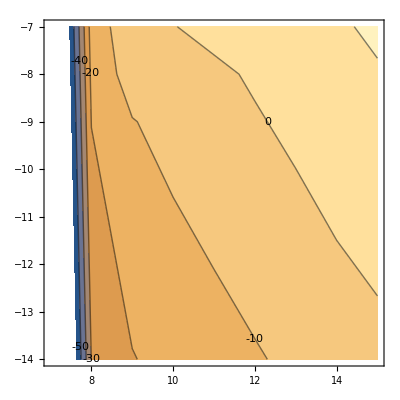

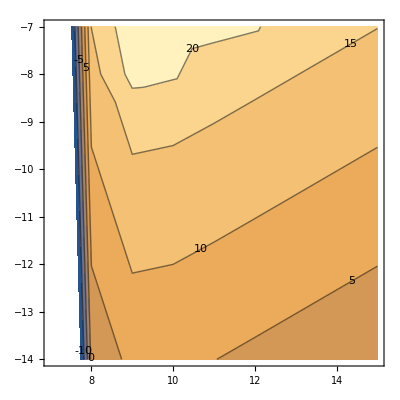

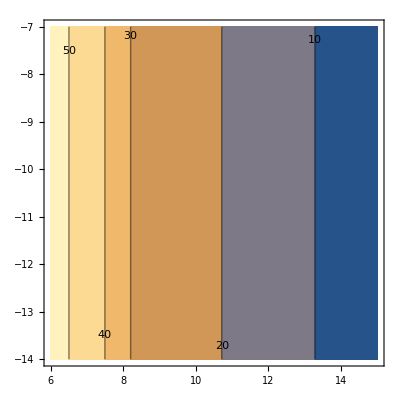

```mathematica
Flatten[Log10@{"mpD"("c")^2/("JpereV"),"κ",("ΓcapE")/("ΓcapP")}/.testgetτsfrompdict/.SIConstRepl,1];
ListContourPlot[%,ContourLabels->All]
Flatten[Log10@{"mpD"("c")^2/("JpereV"),"κ","ΓcapE"}/.testgetτsfrompdict/.SIConstRepl,1];
ListContourPlot[%,ContourLabels->All]
Flatten[Log10@{"mpD"("c")^2/("JpereV"),"κ","ΓcapP"}/.testgetτsfrompdict/.SIConstRepl,1];
ListContourPlot[%,ContourLabels->All]
```

```mathematica
"fD"/.testgetτsfrompdict
```

{{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01},{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01}}

```mathematica
pdicttestlist =Table[Utilities`ReadIt[δScanList[[i]]["file"]][[;;,1,;;]],{i,Length[δScanList]}];
```

```mathematica
Union[Flatten["ϕE"/.pdicttestlist]]
```

{0.,0.0470353,0.0470353,0.164624,0.164624,0.305729,0.305729,0.423318,0.423318,0.465649,0.465649,0.470348,0.470348}

```mathematica
pdicttest =Utilities`ReadIt[δScanList[[1]]["file"]][[;;,1,;;]];
```

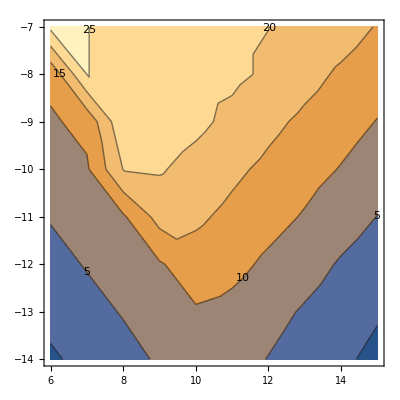

```mathematica
Flatten[Table[Table[Log10@{"mpD"("c")^2/("JpereV"),"κ","dNcMaxdt"}/.pdicttest[[i,j]]/."nD"->naDM[0.01,"mpD"/.pdicttest[[i,j]]],{j,Length[pdicttest[[i]]]}],{i,Length[pdicttest]}]/.SIConstRepl,1];
ListContourPlot[%,ContourLabels->All]
```

#### scrap

```mathematica
{{1, 0 , - βp,0},{0 ,1,0,0},{-βp,0,1,0},{0,0,0,1}}.{{γ, - β γ , 0,0},{-βp  γ,γ ,0,0},{0,0,1,0},{0,0,0,1}}.{t,x,y,z}
Series[%,{βp,0,1}]//Normal
%/.{y->0,t->0,z->0}
%%/.{x->0,t->0,z->0}
```

{-y βp+t γ-x β γ,x γ-t βp γ,y-t βp γ+x β βp γ,z}

{-y βp+t γ-x β γ,x γ-t βp γ,y+βp (-t γ+x β γ),z}

{-x β γ,x γ,x β βp γ,0}

{-y βp,0,y,0}